```mathematica
V=12;
l=5.25;
a=0.305;
s=24.4;
d=17.3;
Plot3D[V/(2Log[(2l-a)/a])Log[(√((x+l)^2+y^2))/(√((x-l)^2+y^2))]+V/2,{x,-s/2,s/2},{y,-d/2,d/2}]
```

-Graphics3D-

```mathematica
ContourPlot[V/(2Log[(2l-a)/a])Log[(√((x+l)^2+y^2))/(√((x-l)^2+y^2))]+V/2,{x,-s/2,s/2},{y,-d/2,d/2},PlotLegends->Automatic,ContourShading->Hue/@Range[0,1,1/40],Contours->30,AspectRatio->Automatic,ColorFunction->Hue]
```

-Graphics-

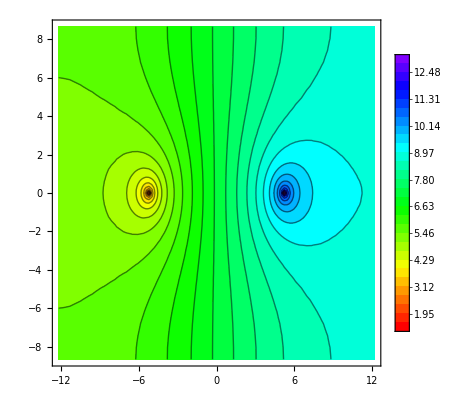

Export::argtu: Export called with 1 argument; 2 or 3 arguments are expected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ContourPlot[∑_(j=-20)^20 (∑_(i=-50)^(+50) (V/(3.8Log[(2l-a)/a])Log[(√((x+l+2*j*s)^2+(y-i*d)^2))/(√((x-l+2*j*s)^2+(y-i*d)^2))]-V/(3.8Log[(2l-a)/a])Log[(√((x+l+(2*j+1)*s)^2+(y-i*d)^2))/(√((x-l+(2*j+1)*s)^2+(y-i*d)^2))]))+V/2+1.776,{x,-s/2,s/2},{y,-d/2,d/2},PlotLegends->Automatic,ContourShading->Hue/@Range[0,1,1/40],Contours->30,ColorFunction->Hue]
```

```mathematica
ζ=0.001;
n=10^-7×10^3×6.02*10^23;
Z=1;
e=1.602*10^-19;
ϵ=8.85*10^-12;
k=1.38*10^-23;
T=300;
```

General::munfl: Exp[-1.01882×10^8] is too small to represent as a normalized machine number; precision may be lost.

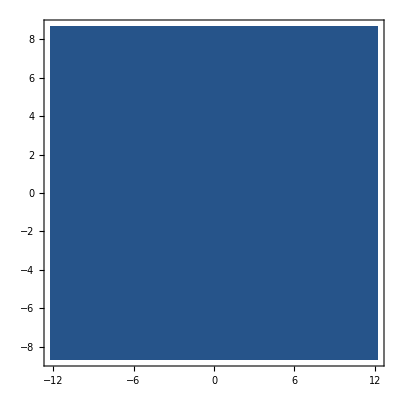

```mathematica
ContourPlot[ζ*Exp[-√((2*n*Z^2*e^2)/(ϵ*k*T))*√((x+l)^2+y^2)],{x,-s/2,s/2},{y,-d/2,d/2}]
```

```mathematica
f[x_,y_]:=∑_(j=-20)^20 (∑_(i=-50)^(+50) (V/(3.8Log[(2l-a)/a])Log[(√((x+l+2*j*s)^2+(y-i*d)^2))/(√((x-l+2*j*s)^2+(y-i*d)^2))]-V/(3.8Log[(2l-a)/a])Log[(√((x+l+(2*j+1)*s)^2+(y-i*d)^2))/(√((x-l+(2*j+1)*s)^2+(y-i*d)^2))]))+V/2+1.776;
V=Table[f[x,y],{x,-s/2,s/2,s/105},{y,-d/2,d/2,d/105}]
```

Table::nliter: Non-list iterator y {-d/2,d/2,d/105} at position 3 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.